# Phase

— Clayton Shonkwiler, May 2025. Supported by NSF DMS–2107700.

The Weierstrass elliptic function ℘ is just about the simplest possible elliptic function, which means it is a doubly-periodic meromorphic function on the complex plane ℂ.

A function f being doubly-periodic means that there exist ω_1,ω_2∈ℂ with ω_1/ω_2∉ℝ so that f(z+ω_1)=f(z) and f(z+ω_2)=f(z) for all z∈ℂ. More generally, this means that f(z+m ω_1+n ω_2)=f(z) for any m,n ∈ℤ, and so the behavior of f is completely determined by what it does on the fundamental domain which is (any translate of) the parallelogram with corners at 0,ω_1,ω_2,ω_1+ω_2. Indeed, if Λ={m ω_1+n ω_2:m,n∈ℤ} is the lattice determined by (ω_1,ω_2), then we can just as well think of f as a function on the quotient space ℂ/Λ, which a topologist or differential geometer would probably call a torus and a number theorist or algebraic geometer would probably call an elliptic curve. This is the source of the name elliptic function.

If a doubly-periodic function f is entire, then it must in particular be continuous and hence bounded on the fundamental domain, and therefore on the entire plane, so Liouville's theorem implies that it must be constant. Therefore, any non-constant doubly-periodic function must have singularities, and the ones with only isolated poles (i.e., the meromorphic ones) are the elliptic functions.

Let γ be the boundary of the fundamental domain of an elliptic function f, oriented clockwise. Then
	
	 0=∮_γ f=∑_(k=1)^n Res_(z=z_k)f(z),
	 
where the first equality follows from double-periodicity (since the values on opposite sides of the fundamental domain are the same, but traversed in opposite directions) and the second equality is the residue theorem (here the sum is over all poles in the fundamental domain). Since the sum of residues can’t be zero if f has a single simple pole, this proves:

Theorem. Any elliptic function has at least 2 poles (counting multiplicity) in its fundamental domain.

If you try to build an elliptic function with a single pole of order 2 at the origin (and hence also at all the lattice points) and so that the leading term in the Laurent series at the origin is 1/z^2, you end up with the Weierstrass function

	℘(z) := 1/z^2+∑_(ω∈Λ\{0}) (1/(z-ω)^2-1/ω^2).

(This is explained very well in sections 1.5–1.6 of Apostol’s Modular Functions and Dirichlet Series in Number Theory.)

Of course, ℘ depends on the periods ω_1 and ω_2 (or equivalently on the lattice Λ), so it is sometimes helpful to indicate it by ℘(z;ω_1,ω_2).

As in Mathematica’s definition WeierstrassP[z, {g_2,g_3}], it is also common to write ℘(z; g_2, g_3), where the invariants g_2 and g_3 are functions of (ω_1,ω_2) (or really of τ=ω_2/ω_1) that show up as coefficients in the Laurent series of ℘ and also in the differential equation ℘'(z)^2=4(℘(z))^3-g_2℘(z)-g_3.

In any case, Mathematica can easily convert between (half-)periods and invariants using WeierstrassInvariants and WeierstrassHalfPeriods.

Here’s a visualization of ℘ on the square lattice using domain coloring, which shows phase as hue and modulus as brightness:

```mathematica
Module[{g2,g3},
{g2,g3}=WeierstrassInvariants[{1/2,I/2}];
Show[ComplexPlot[WeierstrassP[z,{g2,g3}],{z,-2-2I,2+2I},PlotRangePadding->None,BoundaryStyle->None],Graphics[{Thickness[.005],Table[InfiniteLine[{{0,n},{1,n}}],{n,-5,5}],Table[InfiniteLine[{{n,0},{n,1}}],{n,-5,5}]}],PlotRange->2,ImageSize->Large]
]
```

-Graphics-

We can clearly see a double pole at the lattice points (since the colors appear twice in clockwise order) and a double zero in the center of the fundamental domain (again, colors appear twice, but now in counterclockwise order).

And here’s the Weierstrass function for the 60.ba rhombus:

```mathematica
Module[{g2,g3},
{g2,g3}=N[WeierstrassInvariants[{1/2,E^(I π/3)/2}]];
Show[ComplexPlot[WeierstrassP[z,{g2,g3}],{z,-2-2I,2+2I},PlotRangePadding->None,BoundaryStyle->None],Graphics[{Thickness[.005],Table[InfiniteLine[{{0,(√3)/2 n},{1,(√3)/2 n}}],{n,-5,5}],Table[InfiniteLine[{{n,0},{1/2+n,(√3)/2}}],{n,-5,5}]}],PlotRange->2,ImageSize->Large]
]
```

-Graphics-

Notice that we still have the double pole, but the double zero has now split into two simple zeros.

To get a looping animation out of domain coloring plots of Weierstrass functions, one strategy is to find a periodic path in the space of lattices. We can do that using the modular flow, which I previously used to produce this animation.

The idea is to let Λ be the lattice of points of the form P(x
y), where P=(-1 | -√2
1 | -√2) and (x
y)∈ℤ^2 is an integer point in the plane.

```mathematica
P={{-1,-√2},{1,-√2}};
```

Here’s a picture of Λ:

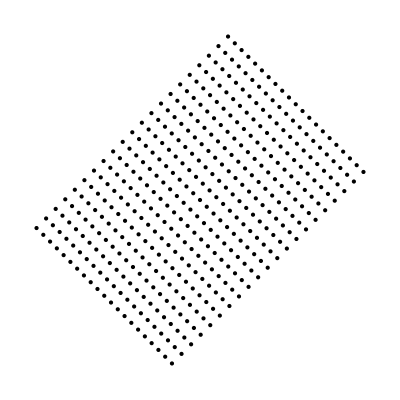

```mathematica
Graphics[{Thickness[.005],PointSize[Large],Table[Point[P.{x,y}],{x,-10,10},{y,-10,10}]},PlotRange->8]
```

And the corresponding tiling by copies of the fundamental domain:

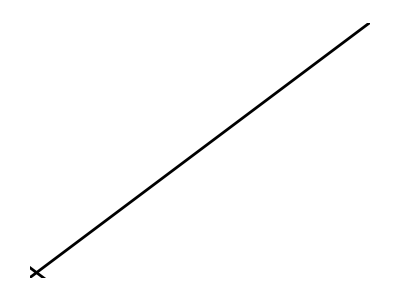

```mathematica
Graphics[{Thickness[.005],Table[InfiniteLine[{P.{0,y},P.{1,y}}],{y,-10,10}],Table[InfiniteLine[{P.{x,0},P.{x,1}}],{x,-10,10}]},PlotRange->8]
```

Now, if we act by matrices of the form (e^s | 0
0 | e^-s) for s∈ℝ, we get a parametrized family of lattices Λ_s whose points are of the form (e^s | 0
0 | e^-s)P(x
y), and this turns out to be 2ln(1+√2)-periodic:

```mathematica
ct[{x_,y_}]:=1/2 Log[(√(x^2-2 √2 x y+2 y^2))/(√(x^2+2 √2 x y+2 y^2))];
DynamicModule[{M,pts},
pts=Append[Quiet[Select[Flatten[Table[{x,y},{x,-30,30},{y,-30,30}],1],Abs[(DiagonalMatrix[{E^ct[#],E^(-ct[#])}].P.#)[[1]]]<=8&]],{0,0}];
Animate[
M=DiagonalMatrix[{E^s,E^-s}].P;
Graphics[{Thickness[.005],PointSize[Large],Point[M.#]&/@pts},PlotRange->8],
{s,0,2Log[1+√2]}]
]
```

Now we download the seasons color palette from Ellert van der Velden’s CMasher:

```mathematica
cols=RGBColor/@Import["https://raw.githubusercontent.com/1313e/CMasher/refs/heads/master/src/cmasher/colormaps/seasons/seasons_norm.txt","Table"];
```

And build the frames of the animation (note that we’re rotating the color palette a quarter turn):

```mathematica
phase=Module[{g2,g3},
ParallelTable[
{g2,g3}=WeierstrassInvariants[N[Complex@@(DiagonalMatrix[{E^s,E^-s}].P.#)]&/@{{1,0},{0,1}}];
ComplexPlot[WeierstrassP[E^(I( π-ArcTan[1/(1+√2)]))z,{g2,g3}],{z,8},ColorFunction->{Blend[cols,Mod[#8-1/4,1]]&,None},Frame->False,PlotRangePadding->None,ImagePadding->None,BoundaryStyle->None,ImageSize->540],
{s,0.,2Log[1+√2]-#,#}]&[2Log[1+√2]/100.]];
```

Which we can export to a GIF:

```mathematica
Export[NotebookDirectory[]<>"phase.gif",phase,"AnimationRepetitions"->Infinity,"DisplayDurations"->1/50];
```

Or visualize directly using ListAnimate:

```mathematica
ListAnimate[phase,50]
```